###    Initialization for plotting

```mathematica
pointList = {};
colorList = {};
```

###    Reading data

```mathematica
adultTrain = SemanticImport["/Users/ebe/Desktop/adultTrain.txt"];
adultTrain = adultTrain[All, <|"age"->1,"workclass"->2,"fnlwgt"->3,"education"->4,"education-num"->5,"marital-status"->6,"occupation"->7,"relationship"->8,"race"->9,"sex"->10,"capital-gain"->11,"capital-loss"->12,"hours-per-week"->13,"native-country"->14,"income"->15|>];
adultTrainBias = adultTrain[Select[#age<30&]];
adultTest = SemanticImport["/Users/ebe/Desktop/adultTest.txt"];
adultTest = adultTest[All, <|"age"->1,"workclass"->2,"fnlwgt"->3,"education"->4,"education-num"->5,"marital-status"->6,"occupation"->7,"relationship"->8,"race"->9,"sex"->10,"capital-gain"->11,"capital-loss"->12,"hours-per-week"->13,"native-country"->14,"income"->15|>];
testIdx=Range[1,Length[adultTest]];
testSet = Normal@adultTest[testIdx,Most@#->Last@#&];
testVal = Normal@adultTest[testIdx,Last];
```

###    The following code is just like a for-loop.
###    for (trainSize = 1000; trainBiasSize = 1000; trainSize <= 8000; trainBiasSize <= 8000; trainSize += 1000; trainBiasSize += 1000) { run SVM algorithm... }
###    However, the code need to be manually run to implement the for-loop.
###    If trainSize or trainBiasSize is beyond 5000, SVM algorithm here is pretty slow; If beyond 10000, the algorithm may cause task abortion.

###    Start of the for-loop

```mathematica
trainSize = 1000;
trainBiasSize = 1000;
```

```mathematica
trainIdx = RandomSample[Range[1,Length[adultTrain]],trainSize];
trainSet=Normal@adultTrain[trainIdx,Most@#->Last@#&];
SVM=Classify[trainSet,Method->"SupportVectorMachine"];
pred = SVM[Normal@adultTest[testIdx,Most]];
{x,y} = {trainSize,Count[MapThread[Equal,{pred,testVal}],False]/Length[testIdx]};
Print["Training set size: ",x,". Error rate: ",y,"."];
pointList = Append[pointList,{x,y}];
colorList = Append[colorList,Blue];
```

Training set size: 5000. Error rate: 827/5427.

```mathematica
trainBiasIdx = RandomSample[Range[1,Length[adultTrainBias]],trainBiasSize];
trainBiasSet=Normal@adultTrainBias[trainBiasIdx,Most@#->Last@#&];
SVMBias = Classify[trainBiasSet,Method->"SupportVectorMachine"];
predBias = SVMBias[Normal@adultTest[testIdx,Most]];
{x,y} = {trainBiasSize,Count[MapThread[Equal,{predBias,testVal}],False]/Length[testIdx]};
Print["Training set size: ",x,". Error rate: ",y,"."];
pointList = Append[pointList,{x,y}];
colorList = Append[colorList,Red];
```

Training set size: 5000. Error rate: 2752/16281.

```mathematica
trainSize = trainSize+1000;
trainBiasSize = trainBiasSize+1000;
```

###    End of the for-loop

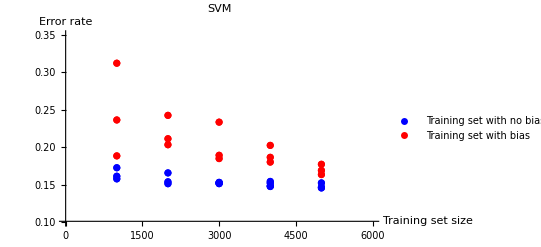

```mathematica
ListPlot[{#}&/@pointList,PlotLegends->PointLegend[{Blue,Red},{"Training set with no bias","Training set with bias"}],AxesLabel->{"Training set size","Error rate"},PlotLabel->"SVM",PlotStyle->colorList,PlotRange->{{0,6000},{0.1,0.35}}]
```

###    Finally, if you have interests in the prediction of your income, your can modify the code down below, and see what you will get.
###    Attribute Information:
 
###    age: continuous. 
###    workclass: Private, Self-emp-not-inc, Self-emp-inc, Federal-gov, Local-gov, State-gov, Without-pay, Never-worked. 
###    fnlwgt: continuous. 
###    education: Bachelors, Some-college, 11th, HS-grad, Prof-school, Assoc-acdm, Assoc-voc, 9th, 7th-8th, 12th, Masters, 1st-4th, 10th, Doctorate, 5th-6th, Preschool. 
###    education-num: continuous. 
###    marital-status: Married-civ-spouse, Divorced, Never-married, Separated, Widowed, Married-spouse-absent, Married-AF-spouse. 
###    occupation: Tech-support, Craft-repair, Other-service, Sales, Exec-managerial, Prof-specialty, Handlers-cleaners, Machine-op-inspct, Adm-clerical, Farming-fishing, Transport-moving, Priv-house-serv, Protective-serv, Armed-Forces. 
###    relationship: Wife, Own-child, Husband, Not-in-family, Other-relative, Unmarried. 
###    race: White, Asian-Pac-Islander, Amer-Indian-Eskimo, Other, Black. 
###    sex: Female, Male. 
###    capital-gain: continuous.   #  income from investment sources, apart from wages/salary
###    capital-loss: continuous.   #  losses from investment sources, apart from wages/salary
###    hours-per-week: continuous. 
###    native-country: United-States, Cambodia, England, Puerto-Rico, Canada, Germany, Outlying-US(Guam-USVI-etc), India, Japan, Greece, South, China, Cuba, Iran, Honduras, Philippines, Italy, Poland, Jamaica, Vietnam, Mexico, Portugal, Ireland, France, Dominican-Republic, Laos, Ecuador, Taiwan, Haiti, Columbia, Hungary, Guatemala, Nicaragua, Scotland, Thailand, Yugoslavia, El-Salvador, Trinadad&Tobago, Peru, Hong, Holand-Netherlands.

```mathematica
predMyIncome = SVM[{<|"age"->26,"workclass"->"Private","fnlwgt"->226802,"education"->"Masters","education-num"->18,"marital-status"->"Never-married","occupation"->"Tech-support","relationship"->"Unmarried","race"->"Other","sex"->"Male","capital-gain"->0,"capital-loss"->0,"hours-per-week"->40,"native-country"->"China"|>}]
```

###    Hope you all can make >50K dollars per year in the future.